# List #4

## Exercise 1

We draw an ellipse:

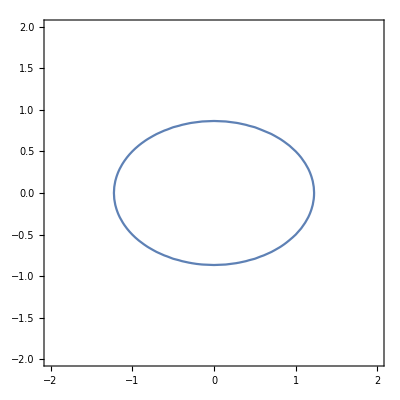

```mathematica
b=3/4;
a=2b;
ContourPlot[x^2/a+y^2/b==1,{x,-2,2},{y,-2,2}]
```

## Exercise 2

We draw Monkey Saddle:

```mathematica
f[x_,y_]:=x y^2-x^3
Animate[Plot3D[f[x,y],{x,-10,10},{y,-10,10},Boxed->True,ViewPoint->{-7Cos[2 Pi k/10], -7 Sin[2 Pi k/10], 3},BoxRatios->{1,1 , 1},Axes->{True,True,False}],{k,1,10},AnimationRate->0.3]
```

## Exercise 3

We draw a little bit modified Monkey Saddle:

```mathematica
g[x_,y_,t_]:=(x+t)(x^2-3 y^2)
saddlelist=Table[Plot3D[g[x,y,t],{x,-10,10},{y,-10,10}],{t,-12,12,1}];
ListAnimate[saddlelist,40,AnimationRate->0.3]
```

## Exercise 4

We compute Van der Pol equation:

{x[t]+0.05 (-1+x[t]^4) x'[t]+x''[t]==0,x'[0]==1.,x[0]==1}

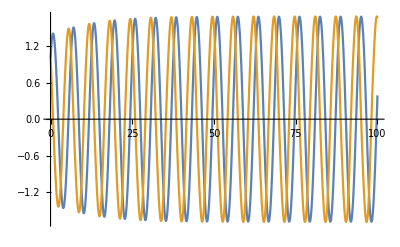

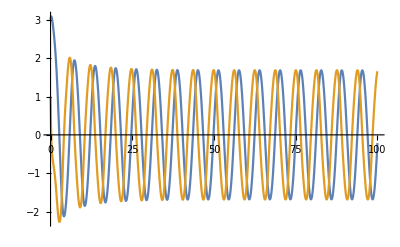

```mathematica
a=1;
ω=1;
ϵ=0.05;
vdp={D[x[t],{t,2}]+ϵ (Power[x[t],2]^2-a)D[x[t],t]+ω^2 x[t]==0,x'[0]==1.0,x[0]==1}
sol=NDSolve[vdp,x,{t,0,100}];
fx1[t_]=x[t]/.sol;
dfx1[t_]=D[fx1[t],t];
Plot[{fx1[t],dfx1[t]},{t,0,100}]

vdp2={D[x[t],{t,2}]+ϵ (Power[x[t],2]^2-a)D[x[t],t]+ω^2 x[t]==0,x'[0]==1.0,x[0]==3};
sol2=NDSolve[vdp2,x,{t,0,100}];
fx2[t_]=x[t]/.sol2;
dfx2[t_]=D[fx2[t],t];
Plot[{fx2[t],dfx2[t]},{t,0,100}]
```

## Exercise 5

We again compute Van der Pol equation, but now in different form:

```mathematica
ClearAll
ϵ=0.5;
vdp51=D[x[t],{t,2}]-ϵ (1-Power[x[t],2])D[x[t],t]+x[t]==0
```

ClearAll

x[t]-0.5 (1-x[t]^2) x'[t]+x''[t]==0

But we can rewrite it as set of equation:

{x'[t]==V[t],V'[t]==-x[t]+0.5 (1-x[t]^2) x'[t]}

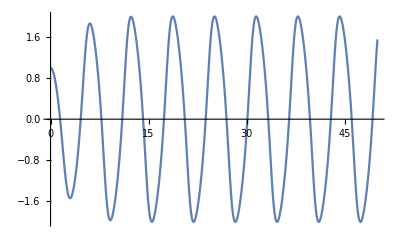
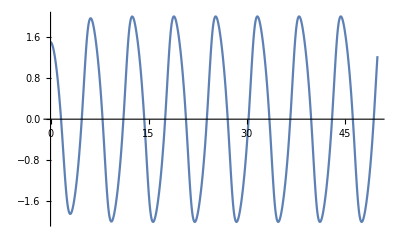
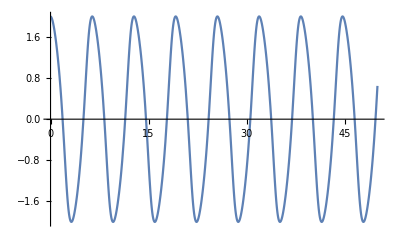
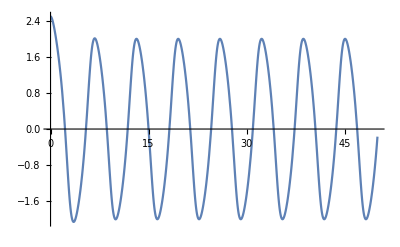
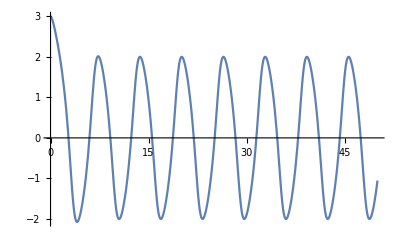

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[V];
vdp52={D[x[t],t]==V[t],D[V[t],t]==ϵ (1-Power[x[t],2])D[x[t],t]-x[t]}
Table[Module[{sol5},sol5=NDSolve[Join[vdp52,{x[0]==xp,V[0]==0}],x,{t,0,50}];
Plot[x[t]/.sol5,{t,0,50}]],{xp,1,3,0.5}]
Table[Module[{sol5b},sol5b=NDSolve[Join[vdp52,{x[0]==RandomReal[0,xp+1],V[0]==0}],x,{t,0,50}];
Plot[x[t]/.sol5,{t,0,50}]],{xp,1,5}]
```

## Exercise 6

We consider movement of projectile thrown with given velocity: